```mathematica
ClearAll["Global`*"];
U1=9.;UD=2.5;ID=25.*10^-3;

IR1=ID
UR1=U1-UD
R1=UR1/IR1
```

0.025

6.5

260.

```mathematica
ClearAll["Global`*"];
R1=220.;UD=2.5;ID=25.*10^-3;

IR1=ID
UR1=ID*R1
U1=UR1+UD
```

0.025

5.5

8.

{c1→47/100000,r1→1000,uz[t]→12 Sin[100 π t]}

{iz[t]==id1[t],id1[t]==ic1[t]+ir1[t],id1[t]==(-1+ⅇ^(19 (u1[t]-u2[t])))/10000000,u2[t]==r1 ir1[t],ic1[t]==c1 u2'[t],uz[t]==u1[t],u2[0]==0}

{{iz[t]→InterpolatingFunction[{{0., 0.06}}, <>][t],id1[t]→InterpolatingFunction[{{0., 0.06}}, <>][t],ir1[t]→InterpolatingFunction[{{0., 0.06}}, <>][t],ic1[t]→InterpolatingFunction[{{0., 0.06}}, <>][t],u1[t]→InterpolatingFunction[{{0., 0.06}}, <>][t],u2[t]→InterpolatingFunction[{{0., 0.06}}, <>][t]}}

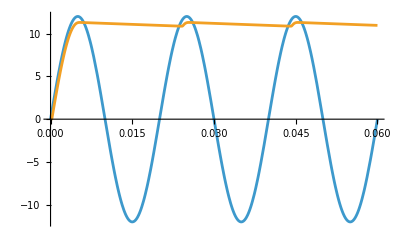

```mathematica
ClearAll["Global`*"];
suciastky={c1->470*10^-6,r1->1*10^3,uz[t]->12*Sin[2*Pi*50*t]}

rovnice={
iz[t]==id1[t],
id1[t]==ir1[t]+ic1[t],

id1[t]==10^-7*(E^(19*(u1[t]-u2[t]))-1),
u2[t]==r1*ir1[t],
ic1[t]==c1*u2'[t],
uz[t]==u1[t],

u2[0]==0
}
nezname={iz[t],id1[t],ir1[t],ic1[t],u1[t],u2[t]};

riesenie=NDSolve[rovnice/.suciastky,nezname,{t,0,3/50}]
Plot[{u1[t]/.riesenie,u2[t]/.riesenie},{t,0,3/50}]
```

```mathematica
ClearAll["Global`*"];
suciastky={U1->50.*10^-3,R1->1.*10^3,R2->100.*10^3,Aop->10.^5};

rovnice={
0==Iz+Ir1,
Ir1==Ir2,
Ir2+Io==0,

Uz==U1,
U1-U2==R1*Ir1,
U2-U3==R2*Ir2,
U3==Aop*(UP-UN),

UP==0,
UN==U2
}

riesenie=Solve[rovnice/.suciastky];
U3/.riesenie[[1]]//EngineeringForm
Ir1/.riesenie[[1]]//EngineeringForm
Ir2/.riesenie[[1]]//EngineeringForm
U3/U1/.riesenie[[1]]/.suciastky//EngineeringForm
```

{0==Ir1+Iz,Ir1==Ir2,Io+Ir2==0,Uz==U1,U1-U2==Ir1 R1,U2-U3==Ir2 R2,U3==Aop (-UN+UP),UP==0,UN==U2}

-4.99496

49.9501×10^-6

49.9501×10^-6

-99.8991

```mathematica
ClearAll["Global`*"];
suciastky={u1[t]->4*Sin[2*Pi*f*t],f->1000,r1->1.*10^3,r2->10.*10^3,Aop->10.^5,c1->160*10^-9};

rovnice={
0==iz[t]+ic1[t],
ic1[t]==ir1[t],
ir1[t]==ir2[t],
ir2[t]==io[t],

uz[t]==u1[t],
ic1[t]==c1*(u1'[t]-u2'[t]),
u2[t]-u3[t]==r1*ir1[t],
u3[t]-u4[t]==r2*ir2[t],
u4[t]==Aop*(0-u3[t]),

u1[0]==0,
u2[0]==0
}
nezname={iz[t],ic1[t],ir1[t],ir2[t],io[t],u2[t],u3[t],u4[t]}
riesenie=NDSolve[rovnice/.suciastky,nezname,{t,0,5/1000},StartingStepSize->10^-9,Method->{"IndexReduction"->Automatic}];
Plot[{u1[t]/.riesenie[[1]],u4[t]/.riesenie[[1]]},{t,0,5/1000}]
```

{0==ic1[t]+iz[t],ic1[t]==ir1[t],ir1[t]==ir2[t],ir2[t]==io[t],uz[t]==u1[t],ic1[t]==c1 (u1'[t]-u2'[t]),u2[t]-u3[t]==r1 ir1[t],u3[t]-u4[t]==r2 ir2[t],u4[t]==-Aop u3[t],u1[0]==0,u2[0]==0}

{iz[t],ic1[t],ir1[t],ir2[t],io[t],u2[t],u3[t],u4[t]}

NDSolve::underdet: There are more dependent variables, {ic1[t],io[t],ir1[t],ir2[t],iz[t],u1[t],u2[t],u3[t],u4[t],uz[t]}, than equations, so the system is underdetermined.

NDSolve::dsvar: 1.02143×10^-7 cannot be used as a variable.

ReplaceAll::reps: {0==ic1[1.02143×10^-7]+iz[1.02143×10^-7],ic1[1.02143×10^-7]==ir1[1.02143×10^-7],ir1[1.02143×10^-7]==ir2[1.02143×10^-7],ir2[1.02143×10^-7]==io[1.02143×10^-7],«3»,u3[1.02143×10^-7]-u4[1.02143×10^-7]==10000. ir2[1.02143×10^-7],u4[1.02143×10^-7]==-100000. u3[1.02143×10^-7],u1[0]==0,u2[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {0.==ic1[1.02143×10^-7]+iz[1.02143×10^-7],ic1[1.02143×10^-7]==ir1[1.02143×10^-7],ir1[1.02143×10^-7]==ir2[1.02143×10^-7],ir2[1.02143×10^-7]==io[1.02143×10^-7],«4»,u4[1.02143×10^-7]==-100000. u3[1.02143×10^-7],u1[0.]==0.,u2[0.]==0.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000102143 cannot be used as a variable.

ReplaceAll::reps: {0==ic1[0.000102143]+iz[0.000102143],ic1[0.000102143]==ir1[0.000102143],ir1[0.000102143]==ir2[0.000102143],ir2[0.000102143]==io[0.000102143],«3»,u3[0.000102143]-u4[0.000102143]==10000. ir2[0.000102143],u4[0.000102143]==-100000. u3[0.000102143],u1[0]==0,u2[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.000204184 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

-Graphics-